solving the reverse kinematics for a two link fully actuated arm. Basically you tell it what x/y coordinates you want to reach and it will give you theta values that allow you to get there

```mathematica
<<ToMatlab`
```

```mathematica
Remove[rx]
rx[θ1_,θ2_]  :=( l1*Cos[θ1] + l2*Cos[θ2 + θ1])
ry[θ1_,θ2_]  :=( l1*Sin[θ1] + l2*Sin[θ2 + θ1])
```

```mathematica
rx[θ1,θ2]^2 + ry[θ1,θ2]^2
```

```mathematica
(l1 Cos[θ1]+l2 Cos[θ1+θ2])^2+(l1 Sin[θ1]+l2 Sin[θ1+θ2])^2 //Expand
```

```mathematica
ReplaceAll[l1^2 Cos[θ1]^2+2 l1 l2 Cos[θ1] Cos[θ1+θ2]+l2^2 Cos[θ1+θ2]^2+l1^2 Sin[θ1]^2+2 l1 l2 Sin[θ1] Sin[θ1+θ2]+l2^2 Sin[θ1+θ2]^2, Cos[θ1+θ2]-> Sin[θ1] *Cos[θ2] +  Cos[θ1]*Sin[θ2]]
```

```mathematica
ReplaceAll[l1^2 Cos[θ1]^2+l1^2 Sin[θ1]^2+2 l1 l2 Cos[θ1] (Cos[θ2] Sin[θ1]+Cos[θ1] Sin[θ2])+l2^2 (Cos[θ2] Sin[θ1]+Cos[θ1] Sin[θ2])^2+2 l1 l2 Sin[θ1] Sin[θ1+θ2]+l2^2 Sin[θ1+θ2]^2, Sin[θ1+θ2]-> Cos[θ1] *Cos[θ2] +  Sin[θ1]*Sin[θ2]]
```

```mathematica
l1^2 Cos[θ1]^2+l1^2 Sin[θ1]^2+2 l1 l2 Cos[θ1] (Cos[θ2] Sin[θ1]+Cos[θ1] Sin[θ2])+l2^2 (Cos[θ2] Sin[θ1]+Cos[θ1] Sin[θ2])^2+2 l1 l2 Sin[θ1] (Cos[θ1] Cos[θ2]+Sin[θ1] Sin[θ2])+l2^2 (Cos[θ1] Cos[θ2]+Sin[θ1] Sin[θ2])^2   //FullSimplify
```

```mathematica
Solve[l1^2+l2^2+2 l1 l2 Sin[θ2]+2 l2 Cos[θ2] Sin[2 θ1] (l1+l2 Sin[θ2]), θ2]
```

Solve[l1^2+l2^2+2 l1 l2 Sin[θ2]+2 l2 Cos[θ2] Sin[2 θ1] (l1+l2 Sin[θ2]),θ2]

```mathematica
rx[θ1,θ2]^2 + ry[θ1,θ2]^2
```

```mathematica
(l1 Cos[θ1]+l2 Cos[θ1+θ2])^2+(l1 Sin[θ1]+l2 Sin[θ1+θ2])^2 //FullSimplify
```

```mathematica
Solve[x^2 + y^2 == l1^2+l2^2+2 l1 l2 Cos[θ2], Cos[θ2]]
```

```mathematica
{{Cos[θ2]->(-l1^2-l2^2+x^2+y^2)/(2 l1 l2)}}
```

```mathematica
c2 = (-l1^2-l2^2+x^2+y^2)/(2 l1 l2)
```

(-l1^2-l2^2+x^2+y^2)/(2 l1 l2)

```mathematica
θ2[x_, y_]  := ArcTan[Sqrt[1 - (-l1^2-l2^2+x^2+y^2)/(2 l1 l2)] , (-l1^2-l2^2+x^2+y^2)/(2 l1 l2)]
```

```mathematica
θ1[x_,y_,θ2_] := ArcTan[y,x] - ArcTan[l2*Sin[θ2], l1 + l2*Cos[θ2]]
```

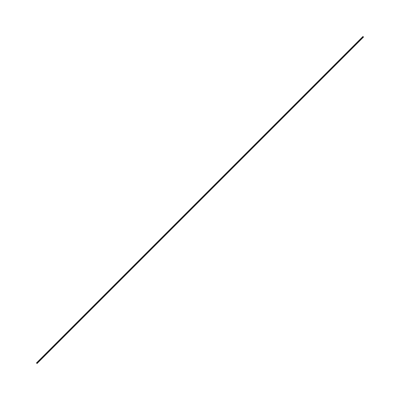

```mathematica
Graphics[Line[{{1,0},{2,1}}]]
```

```mathematica
\n"
```

```mathematica
θ2[x_, y_]  := ArcTan[Sqrt[1 - (-l1^2-l2^2+x^2+y^2)/(2 l1 l2)] , (-l1^2-l2^2+x^2+y^2)/(2 l1 l2)]  
θ1[x_,y_,θ2_] := ArcTan[y,x] - ArcTan[l2*Sin[θ2], l1 + l2*Cos[θ2]]
```

ArcTan[√(1-(-l1^2-l2^2+x^2+y^2)/(2 l1 l2)),(-l1^2-l2^2+x^2+y^2)/(2 l1 l2)]

```mathematica
θ2[x,y] //ToMatlab
```

```mathematica
"atan((1+(-1/2).*l1.^(-1).*l2.^(-1).*((-1).*l1.^2+(-1).*l2.^2+x.^2+ ...\n  y.^2)).^(1/2),(1/2).*l1.^(-1).*l2.^(-1).*((-1).*l1.^2+(-1).*l2.^2+ ...\n  x.^2+y.^2));\n"

θ1[x,y, theta2] //ToMatlab
```

atan((1+(-1/2).*l1.^(-1).*l2.^(-1).*((-1).*l1.^2+(-1).*l2.^2+x.^2+ ...
  y.^2)).^(1/2),(1/2).*l1.^(-1).*l2.^(-1).*((-1).*l1.^2+(-1).*l2.^2+ ...
  x.^2+y.^2));

atan(y,x)+(-1).*atan(l2.*sin(theta2),l1+l2.*cos(theta2));

```mathematica
D[rx[θ1, θ2], θ1]
```

rx^(1,0)[θ1,θ2]

```mathematica
θ1' //FullForm
```

Derivative[1][\[Theta]1]

```mathematica
K[θ1_, θ2_] :=
```